```mathematica
Clear["Global`*"]
```

```mathematica
(* for displaying pendulum *)
pendulum[t_] := { {
Line[{
{0,0},
vk1[t],
vk2[t]
}],
PointSize[.025],
{Red, Point[vk1[t]]},
{Blue, Point[vk2[t]]}
}/.sol/.params }
```

### Double pendulum model

The state vector: q=(θ_1,θ_2)^T - the angular position of the joints
The control inputs:  u=(u_1,u_2)^T- the driving torques at the joints

```mathematica
(* the vectors *)
vq[t_]={θ1[t],θ2[t]};
vu[t_]={u1[t],u2[t]};

(* pendulum parameters *)
params={g->9.81,Subscript[m, 1]->1,Subscript[m, 2]->1,Subscript[l, 1]-> 1,Subscript[l, 2]->1};

(* first link end position - auxiliary for animations *)
vk1[t_]={Subscript[l, 1] Sin[vq[t][[1]]],-Subscript[l, 1]Cos[vq[t][[1]]]};
(* second link end position (output function) - to be controlled *)
vk2[t_]={Subscript[l, 1] Sin[vq[t][[1]]]+Subscript[l, 2] Sin[vq[t][[2]]],-Subscript[l, 1]Cos[vq[t][[1]]]-Subscript[l, 2] Cos[vq[t][[2]]]};

(* dynamics equatations - components *)
mQ={{(Subscript[m, 1]+Subscript[m, 2])Subscript[l, 1]^2,Subscript[m, 2] Subscript[l, 1] Subscript[l, 2] Cos[vq[t][[1]]-vq[t][[2]]]},
	{Subscript[m, 2] Subscript[l, 1] Subscript[l, 2] Cos[vq[t][[1]]-vq[t][[2]]],Subscript[m, 2] Subscript[l, 1]^2}};
mB={{Subscript[m, 2] Subscript[l, 1] Subscript[l, 2](vq'[t][[2]])^2 Sin[vq[t][[1]]-vq[t][[2]]]+g(Subscript[m, 1]+Subscript[m, 2])Subscript[l, 1] Sin[vq[t][[1]]]},
	{-Subscript[m, 2] Subscript[l, 1] Subscript[l, 2](vq'[t][[1]])^2 Sin[vq[t][[1]]-vq[t][[2]]]+g Subscript[m, 2] Subscript[l, 2] Sin[vq[t][[2]]]}};
mQ//MatrixForm    (* let's display *)
mB//MatrixForm

(* the equations - to be simulated *)
eqns=mQ.vq''[t]+mB==vu[t];
Map[MatrixForm,eqns,1]   (* let's display *)
```

(l_1^2 (m_1+m_2) | Cos[θ1[t]-θ2[t]] l_1 l_2 m_2
Cos[θ1[t]-θ2[t]] l_1 l_2 m_2 | l_1^2 m_2)

(g Sin[θ1[t]] l_1 (m_1+m_2)+Sin[θ1[t]-θ2[t]] l_1 l_2 m_2 θ2'[t]^2
g Sin[θ2[t]] l_2 m_2-Sin[θ1[t]-θ2[t]] l_1 l_2 m_2 θ1'[t]^2)

(g Sin[θ1[t]] l_1 (m_1+m_2)+Sin[θ1[t]-θ2[t]] l_1 l_2 m_2 θ2'[t]^2+l_1^2 (m_1+m_2) θ1''[t]+Cos[θ1[t]-θ2[t]] l_1 l_2 m_2 θ2''[t]
g Sin[θ2[t]] l_2 m_2-Sin[θ1[t]-θ2[t]] l_1 l_2 m_2 θ1'[t]^2+Cos[θ1[t]-θ2[t]] l_1 l_2 m_2 θ1''[t]+l_1^2 m_2 θ2''[t])==(u1[t]
u2[t])

SIMULATION FOR U INPUT

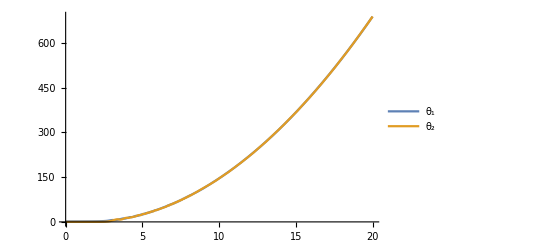

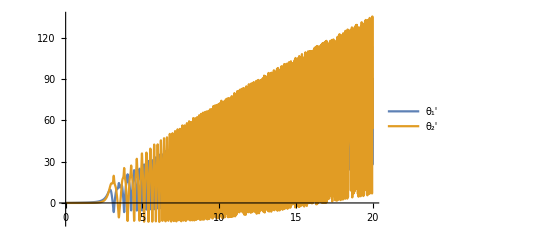

```mathematica
(* some initial conditions *)
ics={θ1[0]==Pi/2,θ2[0]==0,θ1'[0]==0,θ2'[0]==0};

(* temporarily with no controls - observe the behavior with different constat controls *)
(* set of "nice" controls (Subscript[u, 1],Subscript[u, 2])=(5,0),(15,0),(20,0),(0,5) *)
contr={u1[t]->20,u2[t]->0};
(*u1 rusza czerwoną kulką, u2 rusza niebieską (do góry)*)

(* solve and display *)
tmin= 0;
tmax=20;
sol=First[NDSolve[
{eqns,ics}/.params/.contr,
{θ1,θ2},
{t,tmin,tmax}
]];
Plot[Evaluate[vq[t]/.sol],{t,0,tmax},PlotLegends->{"θ_1","θ_2"}]
Plot[Evaluate[vq'[t]/.sol],{t,0,tmax},PlotLegends->{"θ_1'","θ_2'"}]
Animate[
Graphics[
pendulum[t],
PlotRange->{{-2,2},{-2,2}},
Axes->True
],
{t, tmin, tmax, .025},
AnimationRate->1,
AnimationRunning->False
]
```

### Controller (input-output decoulpling - linearization)

The new control inputs:  v=(v_1,v_2)^T

```mathematica
(* the vector *)
vv[t_]={v1[t],v2[t]};

(* the pendulum jacobian matrix (velocity of the second link end) *)
mJ[t_]=D[vk2[t],{vq[t]}];

(* the control loop matrices *)
mD=mJ[t].Inverse[mQ];
mP=mJ'[t].vq'[t]-mJ[t].Inverse[mQ].mB;

(* the linearized equations of dynamics *)
lineqns=(mQ.vq''[t]+mB==-Inverse[mD].mP+Inverse[mD].vv[t]);
Map[MatrixForm,lineqns,1]   (* let's display *)
```

```mathematica
({{g Sin[θ1[t]] Subscript[l, 1] (Subscript[m, 1]+Subscript[m, 2])+Sin[θ1[t]-θnewcontr={v1[t]->0,v2[t]->0};2[t]] Subscript[l, 1] Subscript[l, 2] Subscript[m, 2] θ2'[t]^2+Subscript[l, 1]^2 (Subscript[m, 1]+Subscript[m, 2]) θ1''[t]+Cos[θ1[t]-θ2[t]] Subscript[l, 1] Subscript[l, 2] Subscript[m, 2] θ2''[t]}, {g Sin[θ2[t]] Subscript[l, 2] Subscript[m, 2]-Sin[θ1[t]-θ2[t]] Subscript[l, 1] Subscript[l, 2] Subscript[m, 2] θ1'[t]^2+Cos[θ1[t]-θ2[t]] Subscript[l, 1] Subscript[l, 2] Subscript[m, 2] θ1''[t]+Subscript[l, 1]^2 Subscript[m, 2] θ2''[t]}})==({{((-(Cos[θ1[t]-θ2[t]] Sin[θ1[t]] Subscript[l, 1]^2 Subscript[l, 2] Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)+(Sin[θ2[t]] Subscript[l, 1]^2 Subscript[l, 2] (Subscript[m, 1]+Subscript[m, 2]))/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)) v1[t])/(-(Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 1] Subscript[m, 2])/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]] Sin[θ2[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 1] Subscript[m, 2])/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)-(Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]] Sin[θ2[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]-θ2[t]]^2 Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^3 Subscript[l, 2]^3 Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)-(Cos[θ1[t]] Cos[θ1[t]-θ2[t]]^2 Sin[θ2[t]] Subscript[l, 1]^3 Subscript[l, 2]^3 Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2))+(((Cos[θ1[t]] Cos[θ1[t]-θ2[t]] Subscript[l, 1]^2 Subscript[l, 2] Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)-(Cos[θ2[t]] Subscript[l, 1]^2 Subscript[l, 2] (Subscript[m, 1]+Subscript[m, 2]))/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)) v2[t])/(-(Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 1] Subscript[m, 2])/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]] Sin[θ2[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 1] Subscript[m, 2])/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)-(Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]] Sin[θ2[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]-θ2[t]]^2 Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^3 Subscript[l, 2]^3 Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)-(Cos[θ1[t]] Cos[θ1[t]-θ2[t]]^2 Sin[θ2[t]] Subscript[l, 1]^3 Subscript[l, 2]^3 Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2))-((-(Cos[θ1[t]-θ2[t]] Sin[θ1[t]] Subscript[l, 1]^2 Subscript[l, 2] Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)+(Sin[θ2[t]] Subscript[l, 1]^2 Subscript[l, 2] (Subscript[m, 1]+Subscript[m, 2]))/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)) (-Sin[θ1[t]] Subscript[l, 1] θ1'[t]^2-(-(Cos[θ1[t]] Cos[θ1[t]-θ2[t]] Subscript[l, 1]^2 Subscript[l, 2] Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)+(Cos[θ2[t]] Subscript[l, 1]^2 Subscript[l, 2] (Subscript[m, 1]+Subscript[m, 2]))/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)) (g Sin[θ2[t]] Subscript[l, 2] Subscript[m, 2]-Sin[θ1[t]-θ2[t]] Subscript[l, 1] Subscript[l, 2] Subscript[m, 2] θ1'[t]^2)-Sin[θ2[t]] Subscript[l, 2] θ2'[t]^2-((Cos[θ1[t]] Subscript[l, 1]^3 Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)-(Cos[θ1[t]-θ2[t]] Cos[θ2[t]] Subscript[l, 1] Subscript[l, 2]^2 Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)) (g Sin[θ1[t]] Subscript[l, 1] (Subscript[m, 1]+Subscript[m, 2])+Sin[θ1[t]-θ2[t]] Subscript[l, 1] Subscript[l, 2] Subscript[m, 2] θ2'[t]^2)))/(-(Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 1] Subscript[m, 2])/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]] Sin[θ2[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 1] Subscript[m, 2])/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)-(Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]] Sin[θ2[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]-θ2[t]]^2 Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^3 Subscript[l, 2]^3 Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)-(Cos[θ1[t]] Cos[θ1[t]-θ2[t]]^2 Sin[θ2[t]] Subscript[l, 1]^3 Subscript[l, 2]^3 Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2))-(((Cos[θ1[t]] Cos[θ1[t]-θ2[t]] Subscript[l, 1]^2 Subscript[l, 2] Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)-(Cos[θ2[t]] Subscript[l, 1]^2 Subscript[l, 2] (Subscript[m, 1]+Subscript[m, 2]))/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)) (Cos[θ1[t]] Subscript[l, 1] θ1'[t]^2-(-(Cos[θ1[t]-θ2[t]] Sin[θ1[t]] Subscript[l, 1]^2 Subscript[l, 2] Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)+(Sin[θ2[t]] Subscript[l, 1]^2 Subscript[l, 2] (Subscript[m, 1]+Subscript[m, 2]))/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)) (g Sin[θ2[t]] Subscript[l, 2] Subscript[m, 2]-Sin[θ1[t]-θ2[t]] Subscript[l, 1] Subscript[l, 2] Subscript[m, 2] θ1'[t]^2)+Cos[θ2[t]] Subscript[l, 2] θ2'[t]^2-((Sin[θ1[t]] Subscript[l, 1]^3 Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)-(Cos[θ1[t]-θ2[t]] Sin[θ2[t]] Subscript[l, 1] Subscript[l, 2]^2 Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)) (g Sin[θ1[t]] Subscript[l, 1] (Subscript[m, 1]+Subscript[m, 2])+Sin[θ1[t]-θ2[t]] Subscript[l, 1] Subscript[l, 2] Subscript[m, 2] θ2'[t]^2)))/(-(Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 1] Subscript[m, 2])/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]] Sin[θ2[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 1] Subscript[m, 2])/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)-(Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]] Sin[θ2[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]-θ2[t]]^2 Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^3 Subscript[l, 2]^3 Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)-(Cos[θ1[t]] Cos[θ1[t]-θ2[t]]^2 Sin[θ2[t]] Subscript[l, 1]^3 Subscript[l, 2]^3 Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2))}, {((-(Sin[θ1[t]] Subscript[l, 1]^3 Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)+(Cos[θ1[t]-θ2[t]] Sin[θ2[t]] Subscript[l, 1] Subscript[l, 2]^2 Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)) v1[t])/(-(Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 1] Subscript[m, 2])/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]] Sin[θ2[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 1] Subscript[m, 2])/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)-(Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]] Sin[θ2[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]-θ2[t]]^2 Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^3 Subscript[l, 2]^3 Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)-(Cos[θ1[t]] Cos[θ1[t]-θ2[t]]^2 Sin[θ2[t]] Subscript[l, 1]^3 Subscript[l, 2]^3 Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2))+(((Cos[θ1[t]] Subscript[l, 1]^3 Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)-(Cos[θ1[t]-θ2[t]] Cos[θ2[t]] Subscript[l, 1] Subscript[l, 2]^2 Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)) v2[t])/(-(Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 1] Subscript[m, 2])/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]] Sin[θ2[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 1] Subscript[m, 2])/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)-(Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]] Sin[θ2[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]-θ2[t]]^2 Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^3 Subscript[l, 2]^3 Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)-(Cos[θ1[t]] Cos[θ1[t]-θ2[t]]^2 Sin[θ2[t]] Subscript[l, 1]^3 Subscript[l, 2]^3 Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2))-((-(Sin[θ1[t]] Subscript[l, 1]^3 Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)+(Cos[θ1[t]-θ2[t]] Sin[θ2[t]] Subscript[l, 1] Subscript[l, 2]^2 Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)) (-Sin[θ1[t]] Subscript[l, 1] θ1'[t]^2-(-(Cos[θ1[t]] Cos[θ1[t]-θ2[t]] Subscript[l, 1]^2 Subscript[l, 2] Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)+(Cos[θ2[t]] Subscript[l, 1]^2 Subscript[l, 2] (Subscript[m, 1]+Subscript[m, 2]))/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)) (g Sin[θ2[t]] Subscript[l, 2] Subscript[m, 2]-Sin[θ1[t]-θ2[t]] Subscript[l, 1] Subscript[l, 2] Subscript[m, 2] θ1'[t]^2)-Sin[θ2[t]] Subscript[l, 2] θ2'[t]^2-((Cos[θ1[t]] Subscript[l, 1]^3 Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)-(Cos[θ1[t]-θ2[t]] Cos[θ2[t]] Subscript[l, 1] Subscript[l, 2]^2 Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)) (g Sin[θ1[t]] Subscript[l, 1] (Subscript[m, 1]+Subscript[m, 2])+Sin[θ1[t]-θ2[t]] Subscript[l, 1] Subscript[l, 2] Subscript[m, 2] θ2'[t]^2)))/(-(Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 1] Subscript[m, 2])/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]] Sin[θ2[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 1] Subscript[m, 2])/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)-(Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]] Sin[θ2[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]-θ2[t]]^2 Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^3 Subscript[l, 2]^3 Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)-(Cos[θ1[t]] Cos[θ1[t]-θ2[t]]^2 Sin[θ2[t]] Subscript[l, 1]^3 Subscript[l, 2]^3 Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2))-(((Cos[θ1[t]] Subscript[l, 1]^3 Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)-(Cos[θ1[t]-θ2[t]] Cos[θ2[t]] Subscript[l, 1] Subscript[l, 2]^2 Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)) (Cos[θ1[t]] Subscript[l, 1] θ1'[t]^2-(-(Cos[θ1[t]-θ2[t]] Sin[θ1[t]] Subscript[l, 1]^2 Subscript[l, 2] Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)+(Sin[θ2[t]] Subscript[l, 1]^2 Subscript[l, 2] (Subscript[m, 1]+Subscript[m, 2]))/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)) (g Sin[θ2[t]] Subscript[l, 2] Subscript[m, 2]-Sin[θ1[t]-θ2[t]] Subscript[l, 1] Subscript[l, 2] Subscript[m, 2] θ1'[t]^2)+Cos[θ2[t]] Subscript[l, 2] θ2'[t]^2-((Sin[θ1[t]] Subscript[l, 1]^3 Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)-(Cos[θ1[t]-θ2[t]] Sin[θ2[t]] Subscript[l, 1] Subscript[l, 2]^2 Subscript[m, 2])/(Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)) (g Sin[θ1[t]] Subscript[l, 1] (Subscript[m, 1]+Subscript[m, 2])+Sin[θ1[t]-θ2[t]] Subscript[l, 1] Subscript[l, 2] Subscript[m, 2] θ2'[t]^2)))/(-(Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 1] Subscript[m, 2])/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]] Sin[θ2[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 1] Subscript[m, 2])/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)-(Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]] Sin[θ2[t]] Subscript[l, 1]^5 Subscript[l, 2] Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)+(Cos[θ1[t]-θ2[t]]^2 Cos[θ2[t]] Sin[θ1[t]] Subscript[l, 1]^3 Subscript[l, 2]^3 Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2)-(Cos[θ1[t]] Cos[θ1[t]-θ2[t]]^2 Sin[θ2[t]] Subscript[l, 1]^3 Subscript[l, 2]^3 Subscript[m, 2]^2)/((Subscript[l, 1]^4 Subscript[m, 1] Subscript[m, 2]+Subscript[l, 1]^4 Subscript[m, 2]^2-Cos[θ1[t]-θ2[t]]^2 Subscript[l, 1]^2 Subscript[l, 2]^2 Subscript[m, 2]^2)^2))}})
```

SIMULATION FOR V INPUT (linearized) WITHOUT LOOP

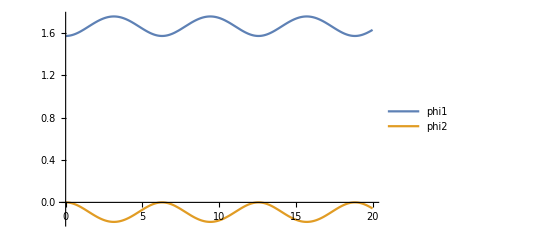

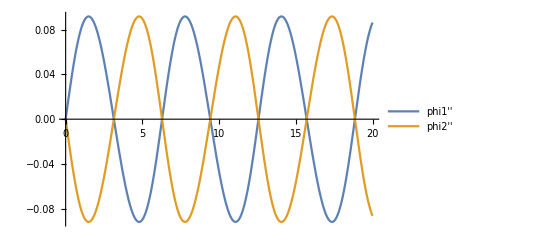

```mathematica
(* some initial conditions *)
ics={θ1[0]==Pi/2,θ2[0]==0,θ1'[0]==0,θ2'[0]==0};

(* initialy with no controls - then observe the behavior with different constat controls *)
(* set of "nice" controls (Subscript[v, 1],Subscript[v, 2])=(0,0),(-0.01,0),(0.01,0),(0,0.01),(-0.1Cos[t],0),(-0.1Sin[t],0),(-0.1Cos[t],0.1Cos[t]) - try the last for the nonzero initial joint speed θ1'[0]==-0.1 *)
(* newcontr={v1[t]->-0,v2[t]->0}; *)
newcontr={v1[t]->-0.1  Cos[t],v2[t]->0.1  Cos[t]};

(*w momencie gdy sterowanie będzie chciało wypchnąć kulke w niedostępne miejsce, HELIKOPTER
v1 steruje (głównie) phi2
v2 steruje (głównie) phi1
konkretnie, phi = całka(v)
*)

(* solve, display, animate, plot pendulum original inputs *)
tmin = 0;
tmax = 20;
sol = First[NDSolve[ 
{lineqns, ics} /. params /. newcontr,
{θ1,θ2},
{t, tmin, tmax}
] ];
Plot[Evaluate[vq[t]/.sol],{t,tmin,tmax},
PlotLegends->{"phi1","phi2"}]
Plot[Evaluate[vq'[t]/.sol],{t,tmin,tmax},
PlotLegends->{"phi1''","phi2''"}]
Animate[
Graphics[
pendulum[t],
PlotRange->{{-2,2},{-2,2}},
Axes->True
],
{t, tmin, tmax, .025},
AnimationRate->1,
AnimationRunning->False
]
```

SIMULATION FOR V INPUT (linearized) WITH CLOSED LOOP

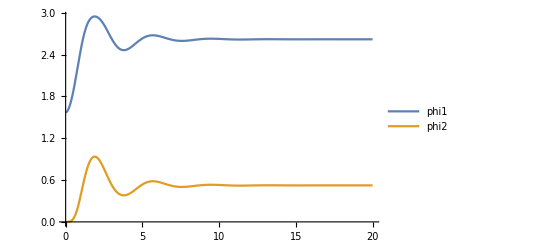

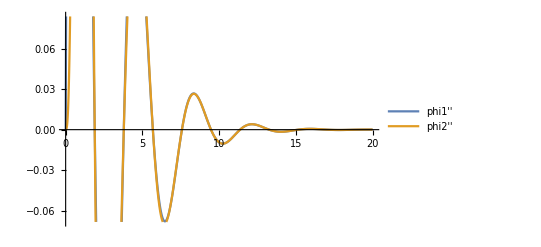

```mathematica
(* some initial conditions - just repeated for convenience *)
ics={θ1[0]==Pi/2,θ2[0]==0,θ1'[0]==0,θ2'[0]==0};

(* the desired trajectory *)
vyd[t_]={0.3+0.3Cos[t],0.3+0.3 Sin[t]};
vyd[t_]={1,0};
(*coordinates of destination trajectory: x,y*)

(* the loop - PD controller *)
K1={{1,0},{0,1}};      (* the gain matrices *)
K0={{3,0},{0,3}};
(*dla K1 = {{1,1}, {1,1}} znowu dostajemy osobliwość
duże wartości np. K1{{200,0},{0,1}} powoduja przesuniecie faktycznej trajektorii, która z czasem zbiega do tej faktycznej
zaczyna kręcić kółka np. na koordynatach -1,1 i powoli przesuwa się (jako całość) do faktycznej
{200,0},{0,1} przesuwa w prawo. {1,0},{0,200} przesuwa w dół
Umiarkowane wartości przyśpieszają stabilizacje na wybranej trajektorii
*)

pdscheme=vyd''[t]-K1.(vk2'[t]-vyd'[t])-K0.(vk2[t]-vyd[t]);
loop=Apply[Rule,{vv[t],pdscheme}//Transpose,1];

(* solve, display, animate, plot pendulum original inputs *)
(* ... *)
tmin = 0;
tmax = 20;
sol = First[NDSolve[ 
{lineqns, ics} /. loop /. params,
{θ1,θ2},
{t, tmin, tmax}
]];
Plot[Evaluate[vq[t]/.sol],{t,tmin,tmax},
PlotLegends->{"phi1","phi2"}]
Plot[Evaluate[vq'[t]/.sol],{t,tmin,tmax},
PlotLegends->{"phi1''","phi2''"}]
expectedTrajectory[t_] := {
Blue, Line[
Map[Function[Evaluate[vyd[#]/. sol]], Range[0,t, 0.025]]
]
};
trace[t_] := {
Purple, Line[
Map[Function[Evaluate[vk2[#]/. params/.sol]], Range[0,t, 0.025]]
]
};
Animate[
Graphics[
{pendulum[t],expectedTrajectory[t],trace[t]},
PlotRange->{{-2,2},{-2,2}},
Axes->True
],
{t, tmin, tmax, .025},
AnimationRate->1,
AnimationRunning->False
]
```